```mathematica
ThreeDiagonalMethod[A_,B_,C_,F_]:=Module[{newB=Table[0,{i,1,Length[B]}],newC=Table[0,{i,1,Length[C]}],newF=Table[0,{i,1,Length[F]}],X=Table[0,{i,1,Length[B]}],α},
newB[[1]]=B[[1]];
newF[[1]]=F[[1]];
Do[
newB[[i]]=B[[i]]-A[[i]]/newB[[i-1]] C[[i-1]];
newF[[i]]=F[[i]]-A[[i]]/newB[[i-1]] newF[[i-1]];
,{i,2,Length[B]}
];
X[[-1]]=newF[[-1]]/newB[[-1]];
Do[
X[[i]]=(newF[[i]]-C[[i]]X[[i+1]])/newB[[i]];
,{i,Length[B]-1,1,-1}
];
Return[X];

]
```

```mathematica
Δx=0.1; Δt=0.05;
```

### Начальные условия

```mathematica
l=1; tmax=1;
f[x_,t_]:=5/(1+(0.05x)^2);
ψ[x_]:=0;
a=1;
```

### Граничные условия

```mathematica
uΓ[x_,0]:=2x(x-1);
uΓ[0,t_]:=Sin[π t];
uΓ[l,t_]:=5t;
```

#### Решение

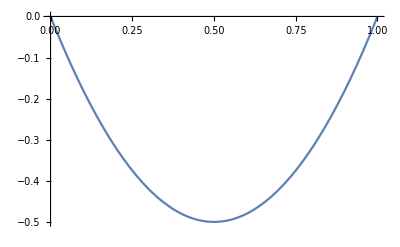

```mathematica
φ=Table[f[i Δx,j Δt],{i,1,l/Δx+1},{j,1,tmax/Δt+1}];
Clear[u];
Do[
u[x,t]:=0;
,{x,2,l/Δx}, {t,2,tmax/Δt}
];

u[x_,1]:=uΓ[(x-1)Δx, 0];
u[1,t_]:=uΓ[0,(t-1)Δt];
u[Round[l/Δx+1],t_]:=uΓ[l,(t-1)Δt];

Plot[Interpolation[Table[{(x-1)Δx,u[x,1]},{x,1,l/Δx+1}]][x],{x,0,l}]
```

```mathematica
α=(a^2 Δt^2)/Δx^2;
u[x_,2]:=Δt ψ[x]+α/2(uΓ[(x+1)Δx]+uΓ[(x-1)Δx])+(1-α)uΓ[x Δx];
ProgressIndicator[Dynamic[(x Δx)/l]]
ProgressIndicator[Dynamic[(k Δt)/tmax]]
Do[
u[x,k+1]=α(u[x+1,k]+u[x-1,k])+2(1-α)u[x,k]-u[x,k-1]+Δt^2 φ[[x,k]];
,{k,2,tmax/Δt+1},{x,2,l/Δx}
]
```

```mathematica
NumericSolution=Table[{(x-1)Δx,u[x,t]},{t,1,tmax/Δt+1}, {x,1,l/Δx+1}];
Manipulate[Plot[Interpolation[NumericSolution[[t]]][x],{x,0,l}], {t, 1, tmax/Δt, 1}]
```

```mathematica
α=(a^2 Δt^2)/Δx^2;
σ=0.;
u[x_,2]:=Δt ψ[x]+α/2(uΓ[(x+1)Δx]+uΓ[(x-1)Δx])+(1-α)uΓ[x Δx];
ProgressIndicator[Dynamic[(x Δx)/l]]
ProgressIndicator[Dynamic[(k Δt)/tmax]]
Aarr={};
Barr={};
Carr={};
Do[AppendTo[Aarr,-σ α],{x,2,l/Δx}];
Do[AppendTo[Barr,1+2σ α],{x,2,l/Δx}];
Do[AppendTo[Carr,-σ α],{x,2,l/Δx}];
Do[
Farr={};
Do[AppendTo[Farr,σ α(u[x+1,k-1]+u[x-1,k-1]-2u[x,k-1])+α(1-2σ)(u[x+1,k]-2u[x,k]+u[x,k-1])+2u[x,k]-2u[x,k-1]+φ[[x,k]] Δt^2],{x,2,l/Δx}];
res=ThreeDiagonalMethod[Aarr,Barr,Carr,Farr];
Do[u[x,k+1]=res[[x-1]],{x,2,l/Δx}];
,{k,2,tmax/Δt}
]
```

```mathematica
u[2,3]
```

0.021678

```mathematica
NumericSolution=Table[{(x-1)Δx,u[x,t]},{t,1,tmax/Δt+1}, {x,1,l/Δx+1}];
Manipulate[Plot[Interpolation[NumericSolution[[t]]][x],{x,0,l}], {t, 1, tmax/Δt, 1}]
```